```mathematica
sRange = 10;
```

```mathematica
κ[s_] = s;
```

```mathematica
ϕ[s_] = Integrate[κ[σ], {σ, 0, s}];
```

```mathematica
Clear[γ]
γ[s_]=γ[s]/.First[NDSolve[{γ'[s]== {Cos[ϕ[s]], Sin[ϕ[s]]},γ[0]=={0, 0}},γ[s],{s,-sRange,sRange}]];
```

```mathematica
(* this is the more intuitive, but amazingly slower way to define γ *)
(* γ[s_]:=Integrate[{Cos[ϕ[σ]], Sin[ϕ[σ]]},{s,-sRange,sRange}]; *)
```

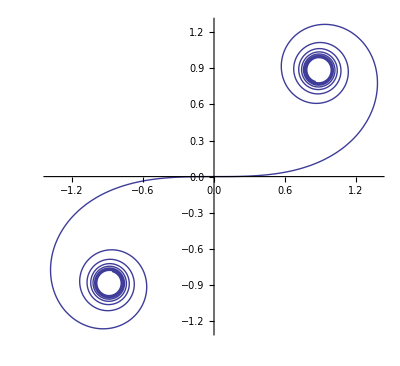

```mathematica
ParametricPlot[γ[s], {s, -sRange, sRange}]
```